# Evolution of Stellar Lifetimes and Effects on Nearby Planets

## Cosmic Billiards

## Kade Vickers, Steven Blodgett, Nate Garey, Carter Garrett

## Constants

```mathematica
SolarMass=1.9891*10^30; (*kg*)
SolarRadius=6.95508*10^8; (*m*)
SolarLuminosity=3.839*10^26; (*W*)
SolarLifetime=86400*365.256308*10*10^9; (*sec*)
SolarTemperature=5777; (*K*)
σ=5.670400*10^-8; (*W m^-2 K^-4*)
G=6.67428*10^-11; (*N m^2 kg^-2*)
```

## HR Diagram

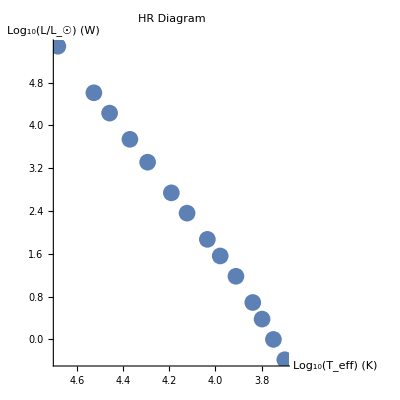

```mathematica
Clear[α,β,γ,L,R,M,Teff]

stellarMasses=SolarMass*{0.8,1,1.25,1.5,2,2.5,3,4,5,7,9,12,15,25};
Rad[M_]:=SolarRadius*α*(M/SolarMass)^β;
Lum[M_]:=SolarLuminosity*(M/SolarMass)^γ;
Time[M_]:=SolarLifetime*(M/SolarMass)^δ;

\[WolframLanguageLogo]=Table[
(*α and β are constants in the Mass-Radius Relation*)
If[
stellarMass<1.66 SolarMass,
α=1.06;
β=0.945;,
α=1.33;
β=0.555;
];
(*γ is a constant in the Mass-Luminosity Relation, and δ is a constant in the Mass-Lifetime Relation*)
If[
stellarMass<0.7 SolarMass,
γ=2.62;
δ=-1.62;,
γ=3.92;
δ=-2.92;
];
R=Rad/@{stellarMass}; (*m*)
L=Lum/@{stellarMass}; (*W*)
(*Stefan-Boltzmann Law: L=4 πσR^2 Subscript[T, eff]^4*)
(*Rearranging: Subscript[T, eff]=(L/(4 πσR^2))^(1/4)*)
τ=Time/@{stellarMass}; (*sec*)
Teff=(L/(4 π σ R^2))^(1/4); (*K*)
{R,L/SolarLuminosity,τ,Teff},
{stellarMass,stellarMasses}
];



\[WolframLanguageLogo]R=Transpose[Transpose[\[WolframLanguageLogo]][[1]]][[1]];
\[WolframLanguageLogo]L=Transpose[Transpose[\[WolframLanguageLogo]][[2]]][[1]];
\[WolframLanguageLogo]τ=Transpose[Transpose[\[WolframLanguageLogo]][[3]]][[1]];
\[WolframLanguageLogo]Teff=Transpose[Transpose[\[WolframLanguageLogo]][[4]]][[1]];



ListPlot[
Transpose[Log10[{\[WolframLanguageLogo]Teff,\[WolframLanguageLogo]L}]],
AspectRatio->1,
PlotRange->All,
Background->White,
BaseStyle->PointSize[0.03],
ColorFunction->Function[{x,y},ColorData["Rainbow"][x]],
PlotLabel->"HR Diagram",
AxesLabel->{"Log_10(T_eff) (K)","Log_10(L/L_☉) (W)"},
ScalingFunctions->{"Reverse",Identity}
]
```

## Hayashi Tracks

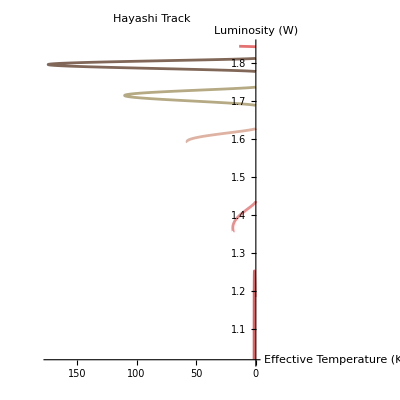

```mathematica
Clear[Teff,Lum]
M=1;

fittingparameters={1,1.6,1.5,2,2,1};
{ξ,η,χ,ζ,ϵ,ω}=fittingparameters;
Teff[t_]:=M^ξ t^η Cos[t]^χ+1/(t! Sin[t]^(1/ζ));
Lum[t_]:=M^ω Sqrt[Log[t]]+(t!)^-ϵ;

ParametricPlot[
{Teff[t],Lum[t]},{t,0,30},
AspectRatio->1,
Background->White,
ColorFunction->Function[{x,y},ColorData["WatermelonColors"][x]],
PlotLabel->"Hayashi Track",
AxesLabel->{"Effective Temperature (K)","Luminosity (W)"},
ScalingFunctions->{"Reverse",Identity}
]



Clear[Teff,Lum]
stellarMasses=SolarMass*{0.8,1,1.25,1.5,2,2.5,3,4,5,7,9,12,15,25};

♚¿=Table[
(*Hayashi Equations*)
fittingparameters={1,1.6,1.5,2,2,1};
{ξ,η,χ,ζ,ϵ,ω}=fittingparameters;
Teff[t_]:=M^ξ t^η Cos[t]^χ+1/(t! Sin[t]^(1/ζ));
Lum[t_]:=M^ω Sqrt[Log[t]]+(t!)^-ϵ;



{ParametricPlot[
{Teff[t],Lum[t]},{t,0,30},
AspectRatio->1,
Background->White,
ColorFunction->Function[{x,y},ColorData["WatermelonColors"][x]],
PlotLabel->"Hayashi Track",
AxesLabel->{"Effective Temperature (K)","Luminosity (W)"},
ScalingFunctions->{"Reverse",Identity}
]},

{M,stellarMasses}
];

Show[♚¿];
```

## Parameters

```mathematica
getParameters[]:= Module[{mass},
mass = Input["Enter a stellar mass, in units of M_⊙"];
Return[mass]
]
(*8 is high mass, < 1.8 is low mass*)
```

## Visual Generation

```mathematica
Heash= SphericalPlot3D[{1,2}, {θ, 0 ,π}, {ϕ, 0 ,3π/2} , PlotStyle->{RGBColor[0.36,0.51,0.69],RGBColor[0.91,0.32,0.18]}, PlotLabel->"H and He Interior"] ;
HeBurn= SphericalPlot3D[{0.5, 1,2}, {θ, 0 ,π}, {ϕ, 0 ,3π/2} , PlotStyle->{RGBColor[0.92,0.83,0.26],RGBColor[0.36,0.51,0.69],RGBColor[0.91,0.32,0.18]}, PlotLabel->"H Interior and He Fusion"] ;
WD = SphericalPlot3D[{0.5, 1}, {θ, 0 ,π}, {ϕ, 0 ,3π/2} , PlotStyle->{RGBColor[0.59,0.88,0.95],RGBColor[0.17,0.89,1]}, PlotLabel->"Carbon Core"];
```

## Low Mass Star

1. (He buildup) Star gets cooler, starts to inflate 
	Goes red, R gets bigger.
2. Helium Flash, carbon ash builds up.
	Gets cooler, smaller drops to that subgiant part. 
3. Eventually, stars blowing off layers 
	Gets much hotter, R slowly decreases. Moves all the way across the top towards planetary nebula. Dims,

```mathematica
firstdredge = Animate[SphericalPlot3D[r,{θ,0,2 π},{ϕ,0,π},Mesh->None,
PerformanceGoal->"Quality",
ColorFunction->(Function[Hue[1/(10+1/7 r),1,1]]),
PlotRange->{{-100,100},{-100,100},{-100,100}}, 
AxesLabel->{"R_⊕"}], 
{r, 3, 90}, 
AnimationRunning->True,
AnimationRate->5];

heliumflash = Animate[
SphericalPlot3D[r,{θ,0,2 π},{ϕ,0,π},Mesh->None,
PerformanceGoal->"Quality",
ColorFunction->(Function[Hue[1/(10+1/7 r),1,1]]),
PlotRange->{{-100,100},{-100,100},{-100,100}}, 
AxesLabel->{"R_⊙"}], 
{r, 90, 10}, 
AnimationRunning->True,
AnimationRate->9];
agb=Animate[SphericalPlot3D[r,{θ,0,2 π},{ϕ,0,π},Mesh->None,
PerformanceGoal->"Quality",
ColorFunction->(Function[Hue[1/(10+1/7 r),1,1]]),
PlotRange->{{-100,100},{-100,100},{-100,100}}, 
AxesLabel->{"R_⊙"}], 
{r, 10, 100}, 
AnimationRunning->True,
AnimationRate->6];

whitedwarf = Animate[SphericalPlot3D[r,{θ,0,2 π},{ϕ,0,π},Mesh->None,
PerformanceGoal->"Quality",
ColorFunction->(Function[Hue[1/(10/6),0.3,1]]),
PlotRange->{{-100,100},{-100,100},{-100,100}}, 
AxesLabel->{"R_⊙"}], 
{r, 10, 5}, 
AnimationRunning->True,
AnimationRate->1];
```

## High Mass Stars

```mathematica
mass15dredge= Animate[SphericalPlot3D[r,{θ,0,2 π},{ϕ,0,π},Mesh->None,
PerformanceGoal->"Quality",
ColorFunction->(Function[Hue[1/(10+1/7 r),1,1]]),
PlotRange->{{-300,300},{-300,300},{-300,300}}, 
AxesLabel->{"R_⊕"}], 
{r, 10, 150}, 
AnimationRunning->False,
AnimationRate->5];
mass15Heflash = 
Animate[SphericalPlot3D[r,{θ,0,2 π},{ϕ,0,π},Mesh->None,
PerformanceGoal->"Quality",
ColorFunction->(Function[Hue[1/(10+1/7 r),1,1]]),
PlotRange->{{-300,300},{-300,300},{-300,300}}, 
AxesLabel->{"R_⊙"}], 
{r, 150, 20}, 
AnimationRunning->False,
AnimationRate->9];
mass15dredge2 = 
Animate[SphericalPlot3D[r,{θ,0,2 π},{ϕ,0,π},Mesh->None,
PerformanceGoal->"Quality",
ColorFunction->(Function[Hue[1/(10+1/7 r),1,1]]),
PlotRange->{{-300,300},{-300,300},{-300,300}}, 
AxesLabel->{"R_⊙"}], 
{r, 20, 200}, 
AnimationRunning->False,
AnimationRate->9];
mass15Cflash = 
Animate[SphericalPlot3D[r,{θ,0,2 π},{ϕ,0,π},Mesh->None,
PerformanceGoal->"Quality",
ColorFunction->(Function[Hue[1/(10+1/7 r),1,1]]),
PlotRange->{{-300,300},{-300,300},{-300,300}}, 
AxesLabel->{"R_⊙"}], 
{r, 200, 30}, 
AnimationRunning->False,
AnimationRate->9];
mass15dredge3 = 
Animate[SphericalPlot3D[r,{θ,0,2 π},{ϕ,0,π},Mesh->None,
PerformanceGoal->"Quality",
ColorFunction->(Function[Hue[1/(10+1/7 r),1,1]]),
PlotRange->{{-300,300},{-300,300},{-300,300}}, 
AxesLabel->{"R_⊙"}], 
{r, 30, 250}, 
AnimationRunning->False,
AnimationRate->9];
mass15neutronStar =
 Animate[SphericalPlot3D[r,{θ,0,2 π},{ϕ,0,π},Mesh->None,
PerformanceGoal->"Quality",
ColorFunction->(Function[Hue[1/(10/6),0.3,1]]),
PlotRange->{{-300,300},{-300,300},{-300,300}}, 
AxesLabel->{"R_⊙"}], 
{r, 30, 25}, 
AnimationRunning->False,
AnimationRate->9];
mass15corecollapse = 
Animate[SphericalPlot3D[{r ,15},{θ,0,2 π},{ϕ,0,π},Mesh->None,
PerformanceGoal->"Quality",
ColorFunction->{(Function[Hue[1/(1+1/60 r),1,1]]),Black},
PlotRange->{{-300,300},{-300,300},{-300,300}}, 
AxesLabel->{"R_⊙"}], 
{r, 200, 0}, 
AnimationRunning->False,
AnimationRate->30]
```

## Main

```mathematica
main[] :=Module[{mass, plotselector},
mass = Input["Enter a stellar mass, in units of M⊙, for either a low or high mass star. (Low mass; M⊙ ≤ 1.2, High Mass; M⊙ ≥ 8"];
plotselector=1;
If[mass <= 1.4, plotselector = ChoiceDialog["Which phase would you like to view?", {"1st Dredge"-> 1, "He Flash"->2 , "AGB"-> 3, "White Dwarf/Nebula"-> 4}]  
];
Print["!!!!!!" ,plotselector];

If[ mass >= 8, 
plotselector = ChoiceDialog["Which phase would you like to view?", {"1st Dredge"-> 5,"2nd Dredge" ->6, "3rd Dredge" ->7, "He Flash"->8 , "C Flash"-> 9, "Neutron Star"-> 10, "Core Collapse"-> 11}, Appearance->"Vertical"->{Automatic, 1}] ;
plotselector
];
(*lowmass section*)
Which[
plotselector==1,
firstdredge,
plotselector==2,
heliumflash,
plotselector == 3 ,
agb,
plotselector==4 ,
whitedwarf
]

Which[
plotselector==1,
Heash,
plotselector==2,
Heash,
plotselector == 3 ,
HeBurn,
plotselector==4 ,
WD
]
Which[
plotselector ==5,
mass15dredge,
plotselector == 6,
mass15dredge2,
plotselector ==7,
mass15dredge3,
plotselector == 8,
mass15Heflash,
plotselector == 9, 
mass15Cflash,
plotselector ==10,
mass15neutronStar,
plotselector == 11,
mass15corecollapse
]
Which[
plotselector== 8,
Heash
]
] 
main[]
```

!!!!!!1

Null^2 -Graphics3D-

## Stellar Death

```mathematica
(* The following few functions are meant to simulate a star with sufficient mass as to collapse in on itself and create a singularity, thus creating a black hole. *)

collapsing =Animate[RegionPlot3D[x^2 + y^2  +z^2 ≤t, {x, -50,50},{ y,-50,50}, {z, -50,50} , MaxRecursion->10,ColorFunction->"AtlanticColors", Mesh->None], {t, 5,10000, 0.1},AnimationDirection->Backward,AnimationRunning->False];

singularity=Animate[Plot3D[-3Exp[0.2*t]Exp[-1/3(x^2+y^2)],{x,-5,5},{y,-5,5},BoxRatios->{1,1,1},PlotRange->{All,All,{-3,3}},Mesh->None,MaxRecursion->10,ColorFunction->"AtlanticColors"],{t,0,20π,0.01},AnimationRunning->False];

ListAnimate[{collapsing,singularity},AnimationRate->0.1]
```

```mathematica
(* Superblast is to show the star going supernova while eradicate is to show the actual explosion, detailed by the dissipation of the "star" if you will *)
superblast = Animate[RegionPlot3D[x^2 + y^2  +z^2 <=t, {x, -50,50},{ y,-50,50}, {z, -50,50} , ColorFunction->"DeepSeaColors", Mesh->None], {t, 5,10000, 0.01},AnimationRunning->False];
eradicate =Animate[RegionPlot3D[x^2 + y^2  +z^2 ≥t, {x, -50,50},{ y,-50,50}, {z, -50,50} , ColorFunction->"DeepSeaColors", Mesh->None], {t, 5,10000, 0.01},AnimationRunning->False];
ListAnimate[{superblast, eradicate}, AnimationRate->0.1]
```

```mathematica
(* The first set of code is meant to simulate the final stages of a medium mass star's life (such as the sun) where it becomes a red giant before becoming a white dwarf. The second function demonstrates the red giant becoming a white dwarf. *)
redgiant =Animate[RegionPlot3D[x^2 + y^2  +z^2 <=t, {x, -50,50},{ y,-50,50}, {z, -50,50} , MaxRecursion->10,ColorFunction->"CherryTones", Mesh->None], {t, 5,10000, 0.1},AnimationRunning->False];
neutronstar=Animate[RegionPlot3D[x^2 + y^2  +z^2 ≤t, {x, -50,50},{ y,-50,50}, {z, -50,50} , MaxRecursion->10,ColorFunction->"Aquamarine", Mesh->None], {t, 5,10000, 0.1},AnimationDirection->Backward,AnimationRunning->False];
ListAnimate[{redgiant, neutronstar},AnimationRate->0.1]
```

## Planetary Aftermath

```mathematica
mlist = {2,1,1,0.4,2};
xlist = {2,4,-1,-4,-0.5};
ylist = {6,0,4,3,-3};

gravpotential = m / Sqrt[x^2+y^2];
n = 5;
Ug = Sum[gravpotential /. {m-> mlist[[i]],x-> x-xlist[[i]], y-> y-ylist[[i]]}, {i,1,n}](*gravitational potential energy equation*)
```

2/(√((-2+x)^2+(-6+y)^2))+1/(√((1+x)^2+(-4+y)^2))+0.4/(√((4+x)^2+(-3+y)^2))+1/(√((-4+x)^2+y^2))+2/(√((0.5+x)^2+(3+y)^2))

```mathematica
Gfield[x_,y_] = Grad[Ug,{x,y}]; (*vector field of acceleration due to gravity*);
Print[Gfield[x,y]];
Gfield[4,4];
empty2DList=Table[ConstantArray[Null,0],{i,5}];
```

{-(2 (-2+x))/(((-2+x)^2+(-6+y)^2)^(3/2))-(1+x)/(((1+x)^2+(-4+y)^2)^(3/2))-(0.4 (4+x))/(((4+x)^2+(-3+y)^2)^(3/2))-(-4+x)/(((-4+x)^2+y^2)^(3/2))-(2 (0.5+x))/(((0.5+x)^2+(3+y)^2)^(3/2)),-(2 (-6+y))/(((-2+x)^2+(-6+y)^2)^(3/2))-(-4+y)/(((1+x)^2+(-4+y)^2)^(3/2))-(0.4 (-3+y))/(((4+x)^2+(-3+y)^2)^(3/2))-y/(((-4+x)^2+y^2)^(3/2))-(2 (3+y))/(((0.5+x)^2+(3+y)^2)^(3/2))}

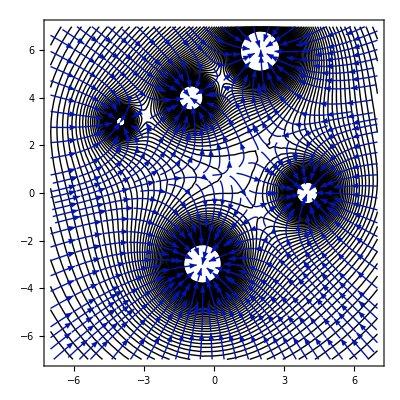

```mathematica
Show[ContourPlot[Ug,{x,-7,7},{y,-7,7},ContourShading->None,Contours->75],StreamPlot[Gfield[x,y],{x,-7,7},{y,-7,7},StreamPoints->Fine]]  (*plots the gravitational wells of some masses and the acceleration due to gravity (the arrows)*)
```

```mathematica
(*now, we just need to take that plot but then animate a movement over time of the velocities of each particle because of the gravitational forces on them.*)
```

```mathematica
(*this function returns a megalist (3D) of lists of x-y coordinates, one for every planet/point mass in the simulation.*)

NBodyGravSim[n_,tmax_,tstep_,masslist_List,startposlist_List,startvlist_List] := Module[{gravpotential,m,Ug,vlist,poslist,func,compiledFunction,compiledGradFunction,gradientsList,mlist,AllGfield,forceValues,tinit=0,t,numcontain,passnum,uglist={},forcefield,ffieldlist = {},finallist},
Block[{x,y},(*make sure that x and y are undefined*)
vlist = startvlist;
poslist = startposlist;
mlist = masslist;
numcontain = tmax/tstep;
finallist=ConstantArray[0,{n,numcontain,2}];

	Do[Module[{answ=0},
Do[
If[i!=k,answ+=mlist[[k]]/Sqrt[(x-poslist[[k,1]])^2+(y-poslist[[k,2]])^2]],{k,n}];
AppendTo[uglist,answ];],
{i,n}]; (*creates a list of potential fields, each one excluding the point it describes*)

Do[forcefield=Grad[uglist[[i]],{x,y}];
AppendTo[ffieldlist,forcefield],{i,n}]; (*creates a list of force vector fields, each one excluding the point it describes*)

(*begin loop to update position and velocities*)
t=tinit;
passnum =1;
While[t<tmax,(*Print["pass started"];*)
	Do[finallist[[i,passnum]]=N[poslist[[i]]],{i,n}]; (*store the position in finallist*)

	forceValues=Table[ffieldlist[[j,1]]/. {x->poslist[[j,1]],y->poslist[[j,2]]},{j,n}];

	Do[vlist[[j,1]]=(forceValues[[j]]/mlist[[j]])+vlist[[j,1]],{j,n}];
	Do[vlist[[j,2]]= (forceValues[[j]]/mlist[[j]])+vlist[[j,1]],{j,n}];
	Do[poslist[[i,1]]=poslist[[i,1]]+vlist[[i,1]]*tstep ,{i,n}]; (*calculate new x pos from old plus x vel * time step, update thing *)
	Do[poslist[[i,2]]=poslist[[i,2]]+vlist[[i,2]]*tstep ,{i,n}]; (*calculate new y pos from old plus y vel * time step, update thing *)
	
	uglist={};
	ffieldlist = {};
	Do[Module[{answ=0},
	Do[
	If[i!=k,answ+=mlist[[k]]/Sqrt[(x-poslist[[k,1]])^2+(y-poslist[[k,2]])^2]],{k,n}];
	AppendTo[uglist,answ];],
	{i,n}]; (*creates a list of potential fields, each one excluding the point it describes*)
	
	Do[forcefield=Grad[uglist[[i]],{x,y}];
	AppendTo[ffieldlist,forcefield],{i,n}]; 

	t= t+tstep;
	passnum +=1;
	Print[t];
	];
];
finallist 
]
```

```mathematica
mysim = NBodyGravSim[3,6,1,{200000000000000,18000000000000,20000000000000},{{-5,-3},{10,10},{0,0}},{{1,2},{-1,0},{0,-1}}];
```

1

2

3

4

5

6

{{{-5.,-3.},{-3.99731,-1.99461},{-2.98867,-0.980036},{-1.95961,0.0694566},{-0.930501,1.09861},{0.0994845,2.12947}},{{10.,10.},{8.97476,8.94952},{7.91559,7.85641},{6.80829,6.701},{5.62532,5.44234},{4.29067,3.95603}},{{0.,0.},{-0.249022,-0.498044},{-1.06457,-1.88012},{-3.88402,-6.70347},{-6.64643,-9.40884},{-9.37389,-12.1014}}}

```mathematica
coordinatesList = mysim;

numTimeSteps=Length[First[coordinatesList]];

colors={Red,Blue,Green};  (*Customize colors as desired*)
pointSizes={0.08,0.05,0.08};

(*Create a list of plots for each time step*)
plotsList=Table[Graphics[Table[{colors[[i]],PointSize[pointSizes[[i]]],Point[coordinatesList[[i,t]]]},{i,Length[coordinatesList]}],PlotRange->{{-20,20},{-20,20}},(*Adjust plot range as needed*)GridLines->{Automatic,Automatic}  (*Adds grid lines to the plot*)],{t,numTimeSteps}];


(*Animate the list of plots*)
ListAnimate[plotsList,AnimationRepetitions->Infinity,AnimationRate->2,AnimationRunning->False]
```